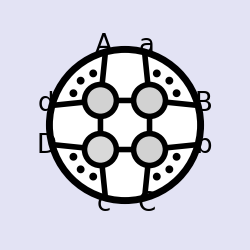
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
n=8;
<<"loop_amplitudes.m";
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y]};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>(Sort[i] Signature[i])/Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
```

```mathematica
n=8;
source=analyticIntegral[scalarBoxExpansion[n+1,2],False];
c1lvan=Table[If[source[[i,2,1,n+1]]===0,i],{i,Length@source}]//Union;
c2lvan=Table[If[source[[i,2,2,n+1]]===0,i],{i,Length@source}]//Union;
c1landc2lvan=Intersection[c1lvan,c2lvan];
c1nvan=Table[If[source[[i,2,1,n]]===0,i],{i,Length@source}]//Union;
c2nvan=Table[If[source[[i,2,2,n]]===0,i],{i,Length@source}]//Union;
c1nandc2nvan=Intersection[c1nvan,c2nvan];
eitherlnonvan=DeleteCases[Union[c1lvan,c2lvan],Null];
eithernnonvan=DeleteCases[Union[c1nvan,c2nvan],Null];
bothnvan=DeleteCases[Intersection[c1nvan,c2nvan],Null];
bothlnonvan=Complement[Range[Length[source]],eitherlnonvan];
bothnnonvan=Complement[Range[Length[source]],eithernnonvan];
bothnlnonvan=Intersection[bothnnonvan,bothlnonvan];
onlyc1lvan=Complement[c1lvan,c1landc2lvan];
onlyc2lvan=Complement[c2lvan,c1landc2lvan];
onlyc1nvan=Complement[c1nvan,c1nandc2nvan];
onlyc2nvan=Complement[c2nvan,c1nandc2nvan];
```

#### Treatment of data1:

```mathematica
rformoc1lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc1lvan,onlyc2nvan],c1nandc2nvan]]]);
rformoc2lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc2lvan,onlyc1nvan],c1nandc2nvan]]]);
data1=Join[rformoc1lvan,{#[[2]],#[[1]],#[[3]]}&/@rformoc2lvan];
```

```mathematica
sixR[cap[{a,b},{c,n,n+1}],x,y,z,w,a];
premovenl[R[a__,n,n+1],R[b___,cap[{c__},{d_,n,n+1}],e___]]:=
If[Length@{b}>0,(-1)^(Length[{b-1}])premovenl[R[a,n,n+1],R[cap[{c},{d,n,n+1}],b,e]],
With[{ints=Intersection[{c},{b,e}]},
If[(Sort[{a}]===Sort[{c,d}])&&(Length@ints==1),
Times@@{R[First[Complement[{a},{d,b,e}]],b,e],
R[First[Complement[{a},{d,b,e}]],cap[Complement[{a},{d}],Complement[{b,e},ints]],d,n,n+1]
},If[Length[ints]==0,premovenl[R[a,n,n+1],#]&/@sixR[b,cap[{c},{d,n,n+1}],e,First[c]],
R[a,n,n+1]R[b,cap[{c},{d,n,n+1}],e]]
]]];premovenl[R[a__,n,n+1],Except[R[___,cap[{__},{_,n,n+1}],___],R[f___]]]:=R[a,n,n+1]R[f];

movenl[Except[_R,z_]*x_R*y_R]:=z If[ContainsAll[List@@x,{n,n+1}],premovenl[x,y],premovenl[y,x]]
```

```mathematica
cdata1=Select[data1,!StringContainsQ[ToString[#],"Sqrt"]&];cdata11=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata1,{_,_,-Li[1]}];cdata12=cdata11[[Complement[Range[Length@cdata11],Flatten[Position[{#[[1]],redR[#[[2]]]/.sortall/.R[1,2,n-1,n,n+1]:>0,#[[3]]}&/@cdata11,{_,0,_}]]]]];cdata13=cdata12[[Complement[Range[Length@cdata12],First/@Position[{#[[1]],Simplify[Limit[(((freduceR[#[[2]]]//fullabB)/.sortall/.Rtodab/.dabBexp)//fullabB)/._R:>0,e->0]],#[[3]]}&/@cdata12,0]]]];cdata14={#[[1]]/.sortcapinR/.{cap[x__,{n-1,n,n+1}]:>cap[x,{1,n-1,n}],cap[x__,{1,n,n+1}]:>cap[x,{1,n-1,n}],cap[{a_,n},{b__,n+1}]:>n}/.cap[{x___,a_,y___},{c___,a_,d___}]:>a,#[[2]]/.cap[{7,8},{x__}]:>7,#[[3]]}&/@cdata13;cdata15=({If[ SubsetQ[Flatten[List@@(#[[1]]/.cap:>List)],{8,9}],premovenl[#[[2]],#[[1]]]/.sortcapinR/.sortR/.toqlog,#[[1]](#[[2]]/.sortcapinR/.sortR/.toqlog)],#[[3]]}&/@cdata14)/.{Qlog[x_/ab[7,8,1,cap[{6,7},y__]]]:>Qlog[x/ab[7,8,1,6]],Qlog[ab[7,8,1,cap[{6,7},y__]]/x_]:>Qlog[ab[7,8,1,6]/x]}/.{Qlog[x_/ab[7,8,1,cap[{1,2},y__]]]:>Qlog[x/ab[7,8,1,2]],Qlog[ab[7,8,1,cap[{1,2},y__]]/x_]:>Qlog[ab[7,8,1,2]/x]};cdata16=(cdata15/.{ab[X,1,2]:>1,ab[X,6,7]:>τ})/.ab[X,a__]:>τ+(ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a]);
```

#### Treatment of data2:

```mathematica
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};

capnlreduce[R1_,R2_]:={R1,R2/.R[a___,cap[{n,n+1},{c__}],d___]:>With[{hh=Intersection[Flatten[{c}],{a,d}]},With[{jj=Complement[{c},hh],kk=Complement[{a,d},hh]},If[Length[hh]==0,R[a,cap[{n,n+1},{c}],d],Switch[Length[hh],
1,(-1)^(Length@{d}-1) R[a,d,cap[jj,Join[hh,{n,n+1}]]] ab@@(Join[kk,{cap[jj,Join[hh,{n,n+1}]]}])/ab@@(Join[kk,{cap[{n,n+1},{c}]}]),
2,R[a,First[jj],d] ab@@(Join[jj,kk,{First@hh}]) ab@@(Join[jj,kk,{Last@hh}]) (ab@@(Join[{n,n+1},hh]))^2/((ab@@(Join[{n+1},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n])) (ab@@(Join[{n+1},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n]))),True,R[a,cap[{n,n+1},{c}],d]]]]]};
```

```mathematica
data2=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[bothnlnonvan]]);
cdata2=Select[data2,!StringContainsQ[ToString[#],"Sqrt"]&];
cdata21=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata2,{_,_,-Li[1]}];
cdata22=Delete[cdata21,{{4},{9},{35},{73},{75},{76}}];
cdata23={#[[1]]#[[2]]/.sortcapinR/.sortR2,#[[3]]}&/@cdata22;
cdata23[[15]]
```

{R[2,3,4,8,9] R[cap[{3,4},{2,8,9}],6,7,8,cap[{8,9},{2,3,4}]],-Li[1]-1/2 log[(ab[2,3,9,1] ab[3,4,8,9])/(ab[2,3,8,9] ab[3,4,9,1])] log[(ab[2,3,4,5] ab[8,9,1,2])/(ab[2,3,8,9] ab[4,5,1,2])]}

replacement rule1

```mathematica
replace1=R[a_,b_,c_,8,9]R[cap[{b_,c_},{a_,8,9}],c_,d_,8,cap[{8,9},{a_,b_,c_}]]:>Which[a===1&&d===7,Qlog[ab[1,2,7,8]/ab[1,b,7,8]] R[1,b,c,7,8]dlog[τ],a===1&&d=!=7,-Qlog[ab[1,b,7,8]/ab[1,d,7,8]] R[1,b,c,d,8]dlog[τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8])],a=!=1&&d===7,Qlog[ab[1,a,7,8]/ab[1,c,7,8]] R[a,b,c,7,8]dlog[τ/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))],a=!=1&&d=!=7,(-Qlog[ab[1,a,7,8]/ab[1,cap[{a,b},{c,d,8}],7,8]]dlog[(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))]+Qlog[ab[1,a,7,8]/ab[1,d,7,8]] dlog[(τ+(ab[1,2,3,8] ab[a,d,7,8])/(ab[1,a,d,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))])R[a,b,c,d,8]];
replace2=R[a_,b_,c_,8,9]R[cap[{a_,b_},{c_,8,9}],1,a_,9,cap[{8,9},{a_,b_,c_}]]:>If[c=!=7,Qlog[ab[1,a,7,8]/ab[1,c,7,8]] R[1,a,b,c,8]dlog[τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8])],Qlog[ab[1,a,7,8]/ab[1,2,7,8]] R[1,a,b,c,8]dlog[τ]];
```

```mathematica
First/@Position[cdata23/.replace1/.replace2,dlog[_]]//Union//Length
```

23

replacement rule2

```mathematica
replace3={R[1,2,3,8,9]R[cap[{2,3},{1,8,9}],3,a_,b_,cap[{8,9},{1,2,3}]]:>-dlog[τ+(-ab[1,2,3,8] ab[3,a,b,7]+ab[1,2,3,7] ab[3,a,b,8])/(ab[1,3,a,b] ab[2,3,7,8])] Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{2,3},{a,b,1}]]] R[1,2,3,a,b],R[c_,d_,7,8,9]R[cap[{c_,d_},{7,8,9}],a_,b_,c_,cap[{8,9},{c_,d_,7}]]:>-Qlog[ab[1,7,8,cap[{c,d},{a,b,7}]]/ab[1,d,7,8]] R[a,b,c,d,7]dlog[τ/(τ+(ab[1,2,3,8] ab[a,b,c,7] ab[c,d,7,8])/(ab[2,3,7,8] (ab[1,c,d,7] ab[a,b,c,8]-ab[1,a,b,c] ab[c,d,7,8])))]};
```

```mathematica
replace4={R[d_,a_,b_,8,9] R[cap[{a_,b_},{d_,8,9}],b_,c_,7,cap[{8,9},{d_,a_,b_}]]:>dlog[(τ+(ab[1,2,3,8] (-ab[d,a,c,7] ab[d,b,7,8]+ab[d,a,7,8] ab[d,b,c,7]))/(ab[2,3,7,8] (-ab[1,d,b,8] ab[d,a,c,7]+ab[1,d,a,8] ab[d,b,c,7])))/(τ+(ab[1,2,3,8] ab[d,a,7,8])/(ab[1,d,a,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,d]/ab[7,8,1,c]] R[d,a,b,c,7]+dlog[(τ+(ab[1,2,3,8] ab[d,a,b,7] ab[b,c,7,8])/(ab[2,3,7,8] (ab[1,b,c,7] ab[d,a,b,8]-ab[1,d,a,b] ab[b,c,7,8])))/(τ+(ab[1,2,3,8] ab[d,a,7,8])/(ab[1,d,a,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,c]/ab[7,8,1,cap[{d,a},{b,c,7}]]] R[d,a,b,c,7],
R[a_,b_,c_,8,9]R[cap[{a_,b_},{c_,8,9}],1,2,a_,cap[{8,9},{a_,b_,c_}]]:>-R[1,2,a,b,c](dlog[(τ+(ab[1,2,3,8] (ab[1,2,b,c] ab[a,c,7,8]-ab[1,2,a,c] ab[b,c,7,8]))/((ab[1,2,b,c] ab[1,a,c,8]-ab[1,2,a,c] ab[1,b,c,8]) ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,c]]+dlog[(τ+(ab[1,2,3,8] (-ab[1,2,a,8] ab[a,b,c,7]+ab[1,2,a,7] ab[a,b,c,8]))/(ab[1,2,a,8] ab[1,a,b,c] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{b,c},{1,2,a}]]/ab[7,8,1,2]]),R[4,5,6,8,9]R[cap[{4,5},{6,8,9}],2,3,4,cap[{8,9},{4,5,6}]]:>Qlog[ab[7,8,1,cap[{2,3},{4,5,6}]]/ab[7,8,1,cap[{5,6},{2,3,4}]]] R[5,6,2,3,4]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,4,8] ab[4,5,6,7]+ab[2,3,4,7] ab[4,5,6,8]))/(ab[2,3,7,8] (ab[1,4,5,6] ab[2,3,4,8]-ab[1,2,3,4] ab[4,5,6,8])))/(τ+(ab[1,2,3,8]ab[5,6,7,8])/(ab[2,3,7,8]ab[1,5,6,8]))]+Qlog[ab[7,8,1,6]/ab[7,8,1,cap[{2,3},{4,5,6}]]] R[5,6,2,3,4]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,5,6] ab[4,6,7,8]+ab[2,3,4,6] ab[5,6,7,8]))/((ab[1,5,6,8] ab[2,3,4,6]-ab[1,4,6,8] ab[2,3,5,6]) ab[2,3,7,8]))/(τ+(ab[1,2,3,8]ab[5,6,7,8])/(ab[2,3,7,8]ab[1,5,6,8]))],R[2,3,4,8,9] R[cap[{3,4},{2,8,9}],4,5,6,cap[{8,9},{2,3,4}]]:>-Qlog[ab[7,8,1,cap[{5,6},{2,3,4}]]/ab[7,8,1,2]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,7,8] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,7,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,5,6]-ab[1,2,3,8] ab[2,4,5,6])))/(τ+1)]-Qlog[ab[7,8,1,cap[{2,3},{4,5,6}]]/ab[7,8,1,cap[{5,6},{2,3,4}]]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,4,8] ab[4,5,6,7]+ab[2,3,4,7] ab[4,5,6,8]))/(ab[2,3,7,8] (ab[1,4,5,6] ab[2,3,4,8]-ab[1,2,3,4] ab[4,5,6,8])))/(τ+1)]};
```

```mathematica
First/@Position[cdata23/.replace3/.replace4,dlog[_]]//Union//Length
```

14

```mathematica
replace5={R[c_,d_,7,8,9] R[cap[{c_,d_},{7,8,9}],a_,b_,9,cap[{8,9},{c_,d_,7}]]:>dlog[τ/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,c]/ab[7,8,1,d]] R[7,cap[{c,d},{7,8,1}],a,b,8],R[1,a_,b_,8,9] R[cap[{a_,b_},{1,8,9}],c_,d_,8,cap[{8,9},{1,a_,b_}]]:>If[d=!=7,-dlog[τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8])] Qlog[ab[7,8,1,a]/ab[7,8,1,b]] R[1,cap[{a,b},{1,8,7}],c,d,8],dlog[τ] Qlog[ab[7,8,1,2]/ab[7,8,1,c]] R[1,a,b,7,8]]};
```

```mathematica
replace6={R[a_,b_,c_,8,9] R[cap[{b_,c_},{a_,8,9}],d_,7,8,cap[{8,9},{a_,b_,c_}]]:>Qlog[ab[7,8,1,a]/ab[7,8,1,d]] (dlog[τ/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] R[a,b,c,7,8]+dlog[(τ+(ab[1,2,3,8] ab[a,b,c,7] ab[a,d,7,8])/(ab[2,3,7,8] (ab[1,a,c,8] ab[a,b,d,7]-ab[1,a,b,8] ab[a,c,d,7])))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] R[a,b,c,d,7]-dlog[(τ+(ab[1,2,3,8] ab[a,d,7,8])/(ab[1,a,d,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] R[a,b,c,d,8]+dlog[(τ+(ab[1,2,3,8] ab[a,c,7,8])/(ab[1,a,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] R[a,c,d,7,8]-dlog[(τ+(ab[1,2,3,8] ab[a,d,7,8] ab[b,c,7,8])/(ab[2,3,7,8] (ab[1,a,c,8] ab[b,d,7,8]-ab[1,a,b,8] ab[c,d,7,8])))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] R[b,c,d,7,8]),R[2,3,4,8,9]R[cap[{3,4},{2,8,9}],5,6,8,cap[{8,9},{2,3,4}]]:>-Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{2,3},{5,6,8}]]]dlog[(τ+1)/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]R[2,3,5,6,8]+Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{2,4},{5,6,8}]]]R[2,4,5,6,8]dlog[(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]+Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{5,6},{2,3,4}]]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,7,8] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,7,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,5,6]-ab[1,2,3,8] ab[2,4,5,6])))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]-Qlog[ab[7,8,1,2]/ab[7,8,1,5]]R[2,3,4,5,8]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,7,8] ab[2,4,5,8]+ab[2,3,5,8] ab[2,4,7,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,5,8]-ab[1,2,3,8] ab[2,4,5,8])))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]+Qlog[ab[7,8,1,2]/ab[7,8,1,6]]dlog[(τ+(ab[1,2,3,8] (-ab[2,3,7,8] ab[2,4,6,8]+ab[2,3,6,8] ab[2,4,7,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,6,8]-ab[1,2,3,8] ab[2,4,6,8])))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]R[2,3,4,6,8]-Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{3,4},{5,6,8}]]]R[3,4,5,6,8]dlog[(τ+(ab[1,2,3,8] (ab[2,4,7,8] ab[3,5,6,8]-ab[2,3,7,8] ab[4,5,6,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[3,5,6,8]-ab[1,2,3,8] ab[4,5,6,8])))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]};
```

```mathematica
cdata24=cdata23/.replace1/.replace2/.replace3/.replace4/.replace5/.replace6;First/@Position[cdata24,dlog[_]]//Union//Length
```

48

```mathematica
replace7={R[1,a_,b_,n,n+1] R[c___,b_,d___,n-1,n,cap[{n,n+1},{1,a_,b_}]]:>Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,c,d]] (dlog[τ] R[1,a,b,n-1,n]-dlog[τ+(ab[1,2,3,8] ab[c,b,d,7,8])/(ab[1,c,b,d,8] ab[2,3,7,8])] R[1,c,b,d,a,n]-dlog[τ+(ab[1,2,3,8] ab[1,a,b,7] ab[c,b,d,7,8])/(ab[1,a,b,8] ab[1,c,b,d,7] ab[2,3,7,8])] R[1,c,b,d,n-1,a]-dlog[τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8])] R[c,b,d,n-1,n,a]),R[1,d___,a_,e___,n+1,cap[{n,n+1},{a_,b_,n-1}]] R[a_,b_,n-1,n,n+1]:>(-1)^(Length[d])Qlog[ab[7,8,1,d,e]/ab[7,8,1,b]] (-dlog[τ] R[1,d,e,a,7,8]-dlog[τ+(ab[1,2,3,8] ab[a,b,7,8] ab[1,d,e,a,7])/(ab[1,a,b,7] ab[2,3,7,8] ab[1,d,e,a,8])] R[1,d,e,a,b,7]+dlog[τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8])] R[1,d,e,a,b,8]+dlog[τ+(ab[1,2,3,8] ab[d,e,a,7,8])/(ab[2,3,7,8] ab[1,d,e,a,8])] R[d,e,a,b,7,8])};
replace8={R[1,2,a_,8,9] R[a_,b_,c_,8,cap[{8,9},{1,2,a_}]]:>-dlog[(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,a,7,8])/(ab[1,2,a,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,b]] R[1,2,a,b,8]+dlog[(τ-(-ab[1,2,3,8] ab[1,a,b,c] ab[2,a,7,8]+ab[1,2,3,8] ab[1,a,7,8] ab[2,a,b,c])/(ab[1,2,a,8] ab[1,a,b,c] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,a,7,8])/(ab[1,2,a,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{2,a},{1,b,c}]]] R[1,2,a,b,c]+dlog[(τ+(ab[1,2,3,8] ab[a,c,7,8])/(ab[1,a,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,a,7,8])/(ab[1,2,a,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,c]] R[1,2,a,c,8]-dlog[τ+(ab[1,2,3,8] ab[2,a,7,8])/(ab[1,2,a,8] ab[2,3,7,8])] Qlog[ab[7,8,1,2]/ab[7,8,1,a]] R[1,a,b,c,8]+dlog[(τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,a,7,8])/(ab[1,2,a,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,a]] R[cap[{2,a},{7,8,1}],1,b,c,8],R[1,a_,b_,9,cap[{8,9},{b_,c_,d_}]]R[b_,c_,d_,8,9]:>-(-dlog[(τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,a]/ab[7,8,1,c]] R[1,a,b,c,8]+dlog[(τ+(ab[1,2,3,8] (ab[1,a,b,d] ab[b,c,7,8]-ab[1,a,b,c] ab[b,d,7,8]))/(ab[1,a,b,8] ab[1,b,c,d] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,a]/ab[7,8,1,cap[{c,d},{1,a,b}]]] R[1,a,b,c,d]+dlog[(τ+(ab[1,2,3,8] ab[b,d,7,8])/(ab[1,b,d,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,a]/ab[7,8,1,d]] R[1,a,b,d,8]-dlog[τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8])] Qlog[ab[7,8,1,a]/ab[7,8,1,b]] R[1,b,c,d,8]-dlog[(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,a]/ab[7,8,1,cap[{c,d},{a,b,8}]]] R[a,b,c,d,8]),R[a_,b_,c_,8,9] R[c_,d_,7,8,cap[{8,9},{a_,b_,c_}]]:>dlog[τ/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,c]/ab[7,8,1,d]] R[a,b,c,7,8]-dlog[(τ-(ab[1,2,3,8] ab[a,b,c,7] ab[c,d,7,8])/(ab[2,3,7,8] (-ab[1,b,c,8] ab[a,c,d,7]+ab[1,a,c,8] ab[b,c,d,7])))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,d]/ab[7,8,1,cap[{a,b},{c,d,7}]]] R[a,b,c,d,7]-dlog[(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{c,d},{a,b,8}]]/ab[7,8,1,d]] R[a,b,c,d,8]+dlog[(τ+(ab[1,2,3,8] ab[a,c,7,8])/(ab[1,a,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,a]/ab[7,8,1,d]] R[a,c,d,7,8]-dlog[(τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,b]/ab[7,8,1,d]] R[b,c,d,7,8]};
replace9={R[c_,d_,7,8,9] R[e_,f_,b_,c_,cap[{8,9},{c_,d_,7}]]:>dlog[τ/(τ+(ab[1,2,3,8] ab[e,f,b,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,f,b}]]))] Qlog[ab[7,8,1,c]/ab[7,8,1,d]] R[e,f,b,c,7]-dlog[(τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[e,f,b,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,f,b}]]))] Qlog[ab[7,8,1,cap[{c,d},{e,f,b}]]/ab[7,8,1,d]] R[e,f,b,c,d]+dlog[(τ+(ab[1,2,3,8] ab[e,f,c,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,f,c}]]))/(τ+(ab[1,2,3,8] ab[e,f,b,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,f,b}]]))] Qlog[ab[7,8,1,cap[{c,d},{e,f,7}]]/ab[7,8,1,d]] R[e,f,c,d,7]-dlog[(τ+(ab[1,2,3,8] ab[e,b,c,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,b,c}]]))/(τ+(ab[1,2,3,8] ab[e,f,b,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,f,b}]]))] Qlog[ab[7,8,1,cap[{c,d},{e,b,7}]]/ab[7,8,1,d]] R[e,b,c,d,7]+dlog[(τ+(ab[1,2,3,8] ab[f,b,c,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{f,b,c}]]))/(τ+(ab[1,2,3,8] ab[e,f,b,7] ab[c,d,7,8])/(ab[2,3,7,8] ab[c,d,7,cap[{1,8},{e,f,b}]]))] Qlog[ab[7,8,1,cap[{c,d},{f,b,7}]]/ab[7,8,1,d]] R[f,b,c,d,7],R[1,a_,b_,9,cap[{8,9},{c_,d_,7}]]R[c_,d_,7,8,9]:>Qlog[ab[7,8,1,c]/ab[7,8,1,d]] (-dlog[τ] R[1,a,b,7,8]+dlog[τ+(ab[1,2,3,8] ab[1,a,b,7] ab[c,d,7,8])/(ab[1,a,b,8] ab[1,c,d,7] ab[2,3,7,8])] R[1,a,b,7,cap[{c,d},{7,8,1}]]+dlog[τ+(ab[1,2,3,8] ab[c,d,7,8])/(ab[1,c,d,8] ab[2,3,7,8])] R[1,a,b,cap[{c,d},{7,8,1}],8]+dlog[τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8])] R[a,b,cap[{c,d},{7,8,1}],7,8]),R[5,6,7,8,9]R[1,2,3,4,cap[{8,9},{5,6,7}]]:>Qlog[ab[7,8,1,5]/ab[7,8,1,6]] (dlog[τ/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] R[1,2,3,4,7]+dlog[(τ+(ab[1,2,3,7] ab[5,6,7,8])/(ab[1,5,6,7] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] R[1,2,3,7,cap[{5,6},{7,8,1}]]-dlog[(τ+(ab[1,2,3,8] ab[1,2,4,7] ab[5,6,7,8])/(ab[1,2,4,8] ab[1,5,6,7] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] R[1,2,4,7,cap[{5,6},{7,8,1}]]+dlog[(τ+(ab[1,2,3,8] ab[1,3,4,7] ab[5,6,7,8])/(ab[1,3,4,8] ab[1,5,6,7] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] R[1,3,4,7,cap[{5,6},{7,8,1}]]-dlog[(τ+(ab[1,2,3,8] ab[2,3,4,7] ab[5,6,7,8])/(ab[2,3,7,8] (ab[1,5,6,7] ab[2,3,4,8]-ab[1,2,3,4] ab[5,6,7,8])))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8])) ]R[2,3,4,7,cap[{5,6},{7,8,1}]])};
replace10={R[e_,f_,a_,8,9]R[a_,b_,c_,8,cap[{8,9},{e_,f_,a_}]]:>dlog[(τ+(ab[1,2,3,8] ab[e,a,7,8])/(ab[1,e,a,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[e,f,7,8])/(ab[1,e,f,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,e]/ab[7,8,1,cap[{e,a},{b,c,8}]]] R[e,a,b,c,8]-dlog[(τ+(ab[1,2,3,8] ab[a,b,7,8])/(ab[1,a,b,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[e,f,7,8])/(ab[1,e,f,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{e,f},{a,b,8}]]/ab[7,8,1,b]] R[e,f,a,b,8]+dlog[(τ+(ab[1,2,3,8] (-ab[e,a,b,c] ab[f,a,7,8]+ab[e,a,7,8] ab[f,a,b,c]))/(ab[2,3,7,8] (-ab[1,f,a,8] ab[e,a,b,c]+ab[1,e,a,8] ab[f,a,b,c])))/(τ+(ab[1,2,3,8] ab[e,f,7,8])/(ab[1,e,f,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{e,f},{a,b,c}]]/ab[7,8,1,cap[{b,c},{e,f,a}]]] R[e,f,a,b,c]-dlog[(τ+(ab[1,2,3,8] ab[a,c,7,8])/(ab[1,a,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[e,f,7,8])/(ab[1,e,f,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,c]/ab[7,8,1,cap[{e,f},{a,c,8}]]] R[e,f,a,c,8]-dlog[(τ+(ab[1,2,3,8] ab[f,a,7,8])/(ab[1,f,a,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[e,f,7,8])/(ab[1,e,f,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,f]/ab[7,8,1,cap[{f,a},{b,c,8}]]] R[f,a,b,c,8]+dlog[(τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[1,b,c,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[e,f,7,8])/(ab[1,e,f,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,b]/ab[7,8,1,c]] R[cap[{b,c},{7,8,1}],e,f,a,8],R[1,2,3,9,cap[{8,9},{4,5,6}]]R[4,5,6,8,9]:>+Qlog[ab[7,8,1,2]/ab[7,8,1,3]] (dlog[(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+1)] R[1,cap[{2,3},{7,8,1}],4,5,8]-dlog[(τ+(ab[1,2,3,8] ab[4,6,7,8])/(ab[1,4,6,8] ab[2,3,7,8]))/(τ+1)] R[1,cap[{2,3},{7,8,1}],4,6,8]+dlog[(τ-ab[1,2,3,cap[{7,8},{4,5,6}]]/(ab[1,4,5,6] ab[2,3,7,8]))/(τ+1)] R[cap[{2,3},{7,8,1}],1,4,5,6]-dlog[(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))/(τ+1)] R[cap[{2,3},{7,8,1}],1,5,6,8]+dlog[τ+1]R[1,4,5,6,8]),R[4,5,6,8,9]R[1,2,3,4,cap[{8,9},{4,5,6}]]:>(-dlog[(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{4,5},{1,2,3}]]/ab[7,8,1,5]] R[1,2,3,4,5]+dlog[(τ+(ab[1,2,3,8] ab[4,6,7,8])/(ab[1,4,6,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{4,6},{1,2,3}]]/ab[7,8,1,6]] R[1,2,3,4,6]+dlog[(τ-(ab[1,2,3,8] ab[1,2,4,cap[{5,6},{4,7,8}]])/(ab[1,2,4,cap[{5,6},{1,4,8}]] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{2,4},{1,5,6}]]] R[1,2,4,5,6]-dlog[(τ+(ab[1,2,3,8] ab[1,3,4,cap[{5,6},{4,7,8}]])/(ab[1,3,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,3]/ab[7,8,1,cap[{5,6},{1,3,4}]]] R[1,3,4,5,6]+dlog[(τ+(ab[1,2,3,8] ab[7,4,8,cap[{5,6},{2,3,4}]])/(ab[1,4,8,cap[{5,6},{2,3,4}]] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,cap[{2,3},{5,6,4}]]/ab[7,8,1,cap[{5,6},{2,3,4}]]] R[2,3,4,5,6]+dlog[(τ+(-ab[1,2,3,8] ab[4,5,6,7]+ab[1,2,3,7] ab[4,5,6,8])/(ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,3]] R[cap[{2,3},{7,8,1}],1,4,5,6])};
```

```mathematica
cdata25=cdata24/.replace7/.replace8/.replace9/.replace10;
```

```mathematica
Complement[Range[88],First/@Position[cdata25,dlog[_]]//Union]
```

{7,12,13,14}

```mathematica
cdata26=cdata25/.R[1,a_,b_,9,cap[{8,9},{a_,b_,c_}]] R[cap[{a_,b_},{1,8,9}],b_,c_,8,9]:>If[c=!=7,Qlog[ab[7,8,1,a]/ab[7,8,1,c]] R[1,a,b,c,8] dlog[τ+(ab[1,2,3,8] ab[b,c,7,8])/(ab[2,3,7,8] ab[1,b,c,8])],-dlog[τ]Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,5,6,7,8]];
```

```mathematica
First/@Position[cdata26,dlog[_]]//Union//Length
```

88

#### Treatment of data3:

```mathematica
(* data3 *)
```

```mathematica
data3=Select[If[ContainsAll[List@@#[[1]],{n,n+1}],{#[[2]],#[[1]],#[[3]]},#]&/@(Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[bothlnonvan,bothnlnonvan],bothnvan]]]),!StringContainsQ[ToString[#],"Sqrt"]&];cdata3=Select[data3,!StringContainsQ[ToString[#],"Sqrt"]&];cdata31=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata3,{_,_,-Li[1]}];cdata32={(#[[1]])/.{R[m___,cap[{n+1,1},a__],b___]:>R[m,cap[{n,1},a],b]}/.sortcapinR/.{R[x___,cap[a__,{1,n,n+1}],y___]:>R[x,cap[a,{1,n,n-1}],y],R[x___,cap[a__,{n-1,n,n+1}],y___]:>R[x,cap[a,{1,n,n-1}],y]}/.sortcapinR/.R[x___,cap[{___,a_,___},{___,a_,___}],y___]:>R[x,a,y]/.sortall/.R[x___,9]:>R[x,8],(#[[2]]/.sortall/.sortcapinR)/.{R[m___,cap[{1,n+1},a__],b___]:>R[m,1,b]}/.R[m___,cap[{n-2,n-1},a__],b___]:>R[m,n-2,b]/.R[x___,cap[a__,{b__,n+1}],y___]:>R[x,cap[a,{b,n}],y],#[[3]]}&/@cdata31;cdata33=DeleteCases[{#[[1]]((#[[2]]/.sortR/.toqlog)/.i_R:>0)/.{Qlog[x_/ab[7,8,1,cap[{6,7},y__]]]:>Qlog[x/ab[7,8,1,6]],Qlog[ab[7,8,1,cap[{6,7},y__]]/x_]:>Qlog[ab[7,8,1,6]/x]}/.{Qlog[x_/ab[7,8,1,cap[{1,2},y__]]]:>Qlog[x/ab[7,8,1,2]],Qlog[ab[7,8,1,cap[{1,2},y__]]/x_]:>Qlog[ab[7,8,1,2]/x]}/.Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]] R[1,i_,j_,7,8]:>0,#[[3]]}&/@cdata32,{0,_}];cdata34=(cdata33/.{ab[X,1,2]:>1,ab[X,6,7]:>τ})/.ab[X,a__]:>τ+(ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a]);
```

```mathematica
(* tree *)
amp1=Total[(rAmp[9,2]/.Join[Table[i->i-1,{i,2,9}],{1->9}]/.Join[Table[i->i-1,{i,2,9}],{1->9}])/.sortR/.toqlog/.R[x___]R[y___]:>0/.{R[x___,cap[{9,1},{b__,8}],y___]:>R[x,8,y]}/.R[x___,cap[a__,{1,9,8}],y___]:>R[x,cap[a,{8,7,1}],y]/.{ab[X,1,2]:>1,ab[X,6,7]:>τ}/.ab[X,a__]:>τ+((ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a])//.capexpand/.sortab)/.sortcapinR/.sortR2]/.R[cap[{a___,x_,b___},{c___,x_,d___}],z___]:>R[x,z]/.sortR2/. Qlog[ab[7,8,1,b_]/ab[7,8,1,a_]] R[cap[{a_,b_},{1,7,8}],c___,a_,d___]:>Qlog[ab[7,8,1,b]/ab[7,8,1,cap[{a,b},{c,d}]]] R[b,c,a,d]//Simplify;
etree92=Total[DeleteCases[DeleteCases[scalarBoxRatioExpansion[9,2]/.onShellGraph[x__][y__]:>0,0]/.i_scalarBox:>First[Flatten[analyticIntegral[i,False]]],amp[9,2]Li[1]]]//Simplify;
data4={amp1,(((etree92/.{Li[1]:>Li[1]/2})//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0)/.amp[9,2]->1};
(*data41=Flatten[Outer[List,List@@amp1,List@@Expand[etree92/.{Li[1]:>Li[1]/2}/.amp[9,2]->1],1],1];
data42={#[[1]],(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@data41;
data43={#[[1]]/.dlog[x_]:>dlog[x/.sortall],(#[[2]]//twistorSimplify)/.sortall}&/@data42;*)
```

```mathematica
data43={#[[1]],data4[[2]]}&/@(List/@Expand[data4[[1]]]);
```

```mathematica
(* easy 4 massbox *)
easy4massbox={{dlog[τ]R[8,2,3,4,5]Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{4,5},{2,3,8}]]],Li[1]-Li[1-(ab[2,3,4,5] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,4,5])]-Li[1-(ab[4,5,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,4,5])]+log[1-(ab[2,3,4,5] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,4,5])] log[1-(ab[4,5,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,4,5])]-1/2 log[(ab[2,3,4,5] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,4,5])] log[(ab[4,5,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,4,5])]},{Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{5,6},{2,3,8}]]]R[8,2,3,5,6]dlog[τ],Li[1]-Li[1-(ab[2,3,5,6] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,5,6])]-Li[1-(ab[5,6,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,5,6])]+log[1-(ab[2,3,5,6] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,5,6])] log[1-(ab[5,6,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,5,6])]-1/2 log[(ab[2,3,5,6] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,5,6])] log[(ab[5,6,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,5,6])]},{dlog[τ]R[8,3,4,5,6]Qlog[ab[7,8,1,2]/ab[7,8,1,cap[{5,6},{3,4,8}]]],Li[1]-Li[1-(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6])]-Li[1-(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6])]+log[1-(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6])] log[1-(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6])]-1/2 log[(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6])] log[(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6])]}};
data5={#[[1]]//dabRcanel,((#[[2]])//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@easy4massbox;
```

```mathematica
(* Divergent part of the second term *)
```

```mathematica
secpart={FirstCase[#,_R,Infinity],#/FirstCase[#,_R,Infinity]}&/@Flatten[scalarBoxExpansion[8,1]/.onShellGraph[x_][y__]:>rForm[onShellGraph[x][y]]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]]];
secpart=(R[2,6,7,8,9]/.toqlog/.{ab[X,1,2]:>1,ab[X,6,7]:>τ}/.ab[X,a__]:>τ+((ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a])//.capexpand/.sortab))(Total[Times@@#&/@(DeleteCases[secpart,{_,-Li[1]|Li[1]}]/.{Li[1]->Li[1]/2})]+Total@DeleteCases[(DeleteCases[scalarBoxRatioExpansion[8,1]/.onShellGraph[x_][y__]:>0,0]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]])/amp[8,1],Li[1]]Total[rAmp[8,1]]);
data6={secpart[[1;;2]]#[[1]],#[[2]]}&/@(Reverse[List@@Collect[#,_R]]&/@(List@@(secpart[[3]])));
```

```mathematica
(*coefficents of 1/τ in hard4massbox*)
hardlogt={{Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]dlog[τ],-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[1,2,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[4,5,7,8])])log[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]},
{Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,3,4,7]dlog[τ],-Li[1-(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]-1/2(log[τ]+log[(ab[1,2,3,4]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[3,4,7,8])])log[(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]},
{ Qlog[ab[7,8,1,cap[{2,3},{4,5,7}]]/ab[7,8,1,6]] R[2,3,4,5,7]dlog[τ],-Li[1-(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[2,3,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[2,3,6,7]ab[4,5,7,8])])log[(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]}};
(*divergent part of hardbox @ tau-> infnity *)
hardloginf={{-Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]dlog[τ+1],-Li[1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])]-1/2 log[(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])] (log[(ab[1,2,3,8] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])]-log[τ])},{-Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,3,4,6,7]dlog[τ+1],-Li[1-(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])]-1/2 log[(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])] (log[(ab[1,2,3,8] ab[1,2,7,8] ab[3,4,6,7])/(ab[1,2,6,7] ab[1,3,4,8] ab[2,3,7,8])]-log[τ])},{Qlog[ab[7,8,1,cap[{5,6},{3,4,1}]]/ab[7,8,1,2]] R[1,3,4,5,6]dlog[τ+1],-Li[1-(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])]-1/2 log[(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])](log[(ab[1,2,3,8] ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[1,3,4,8] ab[2,3,7,8])]-log[τ])}}
```

{{-dlog[1+τ] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7],-Li[1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])]-1/2 log[(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])] (-log[τ]+log[(ab[1,2,3,8] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])])},{-dlog[1+τ] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,3,4,6,7],-Li[1-(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])]-1/2 log[(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])] (-log[τ]+log[(ab[1,2,3,8] ab[1,2,7,8] ab[3,4,6,7])/(ab[1,2,6,7] ab[1,3,4,8] ab[2,3,7,8])])},{dlog[1+τ] Qlog[ab[7,8,1,cap[{5,6},{3,4,1}]]/ab[7,8,1,2]] R[1,3,4,5,6],-Li[1-(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])]-1/2 log[(ab[1,2,3,4] ab[1,5,6,8])/(ab[1,2,5,6] ab[1,3,4,8])] (-log[τ]+log[(ab[1,2,3,8] ab[1,2,7,8] ab[3,4,5,6])/(ab[1,2,5,6] ab[1,3,4,8] ab[2,3,7,8])])}}

```mathematica
(*(* coefficients of 1/τ *)
temp1=(Limit[#,τ->0]&/@(τ#[[1]]&/@data13)).(Last/@data13);
temp2=Limit[#[[1]]τ,τ->0]&/@data28;
(* Position[temp22,Indeterminate]//Flatten *)
(* {18,31,40} *)
temp2=ReplacePart[temp2,{18->(SeriesCoefficient[τ data27[[18,1]],{τ,0,0}]/.sortall/.{R[1,2,3,6,7]->sixR[1,2,3,6,7,8]}/.sortall//dabRcanel)/.sortall,
31->(SeriesCoefficient[τ data27[[31,1]],{τ,0,0}]/.sortall/.{R[2,3,6,7,8]->sixR[2,3,6,7,8,4]})/.sortall//Simplify//dabRcanel,
40->(SeriesCoefficient[τ data27[[40,1]],{τ,0,0}]/.sortall/.{R[3,4,5,6,7]->sixR[3,4,5,6,7,8]}/.sortall//dabRcanel)/.sortall}].(Last/@data28);
temp3=((Limit[#,τ->0]&/@(τ#[[1]]&/@data33))/.dab[x___,cap[a__,{b___,9,c___}],y___]:>dab[x,cap[a,{b,8,c}],y]).(Last/@data33);
temp4=Limit[τ data4[[1]],τ->0](Last@data4);
tempeasy=(Limit[τ #[[1]],τ->0]&/@data5).data5[[All,2]];
temphard=(Limit[τ #[[1]],τ->0]&/@hardlogt).hardlogt[[All,2]];
tempsec=Limit[τ secpart,τ->0]//dabRcanel;*)
```

```mathematica
(*(* check 1/tau and log[tau]/tau *)
minideg[f_,var_]:=minideg[f,var]=If[SeriesCoefficient[f,{var,0,0}]===0,minideg[D[f,var],var]+1,0]
tempall=(temp1+temp2+temp3+temp4+tempeasy+temphard-tempsec)/.{log[x_]:>(log[0]minideg[x,τ]+log[SeriesCoefficient[x,{τ,0,minideg[x,τ]}]])}/.Li[x_]:>Li[Limit[x,τ->0]]/.{log[1]->0,Li[0]->0};*)
```

```mathematica
(*Table[numtemp=(((tempall//neab1)//todoubleab//todmatrix//fuse)/.dabne[{1,2}]/.DmatrixEval3[{3,i,j},3])//neab1;
(numtemp/.{log[0]->0}/.log->Log/.Li[x_]:>PolyLog[2,x])//FullSimplify,{i,1,8},{j,1,i}]*)
```

```mathematica
(*(* log e num check *)
logecoeff[exp_]:=D[exp/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>a log[e]+log[b],log[e]]/.log[x__]:>log[Limit[x,e->0]];

data12=({#[[1]]#[[2]],#[[3]]}&/@data12);
data32=({#[[1]]#[[2]],#[[3]]}&/@data32);
logedata1=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data12];
logedata2=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data25];
logedata2=logedata2/.{R[x___,cap[{y__},{7,8,9}],z___]:>R[x,cap[{y},{7,8,1}],z],R[x___,cap[{y__},{1,8,9}],z___]:>R[x,cap[{y},{7,8,1}],z]}/.R[x___,cap[{y__},{a_,8,9}],z___]:>R[x,cap[{y},{a,8,B}],z];
logedata3=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data32];
treeresult=2 *amp2  log[(τ ab[1,2,3,8] ab[5,6,7,8])/((1+τ) (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))];
loge4massbox=Total[Total[{#[[1]]logecoeff[#[[2]]//fullabB]}&/@easy4massbox]];*)
```

```mathematica
logecoeff[exp_]:=D[exp/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>a log[e]+log[b],log[e]]/.log[x__]:>log[Limit[x,e->0]];
randomPositiveZs[20]
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧]
```

```mathematica
(*echeck=cdata16[[All,1]].((cdata16[[All,2]]//fullabB)//logecoeff)+cdata26[[All,1]].((cdata26[[All,2]]//fullabB)//logecoeff)+cdata34[[All,1]].((cdata34[[All,2]]//fullabB)//logecoeff)+2 *amp1  log[(τ ab[1,2,3,8] ab[5,6,7,8])/((1+τ) (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]+easy4massbox[[All,1]].((easy4massbox[[All,2]]//fullabB)//logecoeff);*)
```

```mathematica
(*Do[
If[Union[#]=={0},Print[i," ",j];,Print["error|",i,j]]&@With[{hh=((echeck/.sortab/.qlogtodab//neabp)//todoubleab//todmatrix//fuse)/.dabne[{1,3}]},
Flatten@ParallelTable[temp=Integrate[Collect[Expand[((hh/.DmatrixEval3[{a,b,c},3]//neabp//Simplify)/.Log->log)//expandlog],_log]/.log->Log/.dlog[x_]:>D[Log[x],τ]//Simplify,τ];FullSimplify[Limit[temp,τ->0]-Limit[temp,τ->Infinity]],{a,2},{b,a,2},{c,b,2}]],{i,2},{j,i+1,2}]*)
```

```mathematica
cdata123=Join[cdata16,cdata26,cdata34];
cdata123={#[[1]],((#[[2]]/.Li[1]:>Li[1]/2)//fullabB)/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>log[b]/.{Li[x__]:>Li[Limit[x,e->0]],log[x__]:>log[Limit[x,e->0]]}}&/@cdata123;
```

Part::partd: 部分指定 cdata16⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 cdata16⟦2⟧ 比对象深度更长.

Part::partd: 部分指定 cdata26⟦1⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

```mathematica
(*cdata123456=Join[cdata123,data43,data5,data6];*)
cdata123456=Join[<<"cdata123",data5];
dlogtaupart=Join[{{D[data4[[1]],dlog[τ]],Expand[data4[[2]]/.log[x_]:>logmonic[x]/.log[1]->0]}},Expand[({D[#[[1]],dlog[τ]],#[[2]]}&/@(cdata123456/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]}))]]/.log[x_]log[y_]:>With[{hh=Limit[x,τ->0],jj=Limit[y,τ->0]},Which[hh===0&&(!(jj===1)),log[x]log[y/jj]+log[x/τ]log[jj],jj===0&&(!(hh===1)),log[y]log[x/hh]+log[y/τ]log[hh],(hh===0&&jj===1)||(hh===1&&jj===0),log[x]log[y],True,log[x]log[y]]]/.log[1]->0;
(*logpart={#[[1]]dlog[τ],#[[2]]}&/@(Join[{{D[data4[[1]],dlog[τ]],Expand[data4[[2]]/.log[x_]:>logmonic[x]/.log[1]->0]}},Expand[({D[#[[1]],dlog[τ]],#[[2]]}&/@(cdata123456/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]}))]]/.log[x_]log[y_]:>With[{hh=Limit[x,τ->0],jj=Limit[y,τ->0]},If[(hh===0&&jj===1)||(hh===1&&jj===0),log[x]log[y],0]]/.{log[1]->0,_Li->0});*)
ndlogtaupart=Join[({#,Expand[data4[[2]]/.log[x_]:>logmonic[x]/.log[1]->0]}&/@(List@@(data4[[1]]/.dlog[τ]->0))),{#[[1]]/.dlog[τ]:>0,#[[2]]}&/@(cdata123456/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]})];
dlogtaupart1=({#[[1]],#[[2]]-(Expand[#[[2]]]/.log[τ]log[x_]:>doublelog[τ,x]/.{Li[x__]:>Li[Limit[x,τ->0]],log[x_]:>log[Limit[x,τ->0]]})}/.{Li[0]->0,log[1]->0}&/@DeleteCases[dlogtaupart,{0,_}]//Simplify)/.{log[x_]-log[y_]:>log[x/y],doublelog[τ,x_]:>log[τ]log[x]}//Simplify;
```

```mathematica
(*{dlog[τ]#[[1]],#[[2]]}&/@DeleteCases[dlogtaupart1,{0,_}|{_,0}],*)
```

```mathematica
substract1=Join[{dlog[τ]#[[1]],#[[2]]}&/@DeleteCases[dlogtaupart1,{0,_}|{_,0}],DeleteCases[ndlogtaupart,{0,_}|{_,0}]];//AbsoluteTiming
substract2=substract1/.dlog[x_]:>If[Limit[1/x,τ->+Infinity]===0,dlog[x/(τ+1)],dlog[x]]/.dlog[1]->0;
substract3=substract1/.dlog[x_]:>If[Limit[1/x,τ->+Infinity]===0,dlog[τ+1],0]/.dlog[1]->0;
```

{0.0033354,Null}

```mathematica
diffdoublelog[x_,y_]:=With[{hh=Limit[x,τ->Infinity],jj=Limit[y,τ->Infinity]},
Which[hh===0,log[τ x]log[y]-log[τ]log[y],hh===∞||hh===-∞,log[x/τ]log[y]+log[τ]log[y],jj===0,log[τ y]log[x]-log[τ]log[x],jj===∞||jj===-∞,log[y/τ]log[x]+log[τ]log[x],True,log[x]log[y]]]/.log[1]->0
finiteanddiv=(Total/@Transpose@({{#[[1]]-#[[2]],#[[2]]}&@{#/.{_log->0},#/.{_log->0}/.Li[x_]:>Li[Limit[x,τ->Infinity]]}/.Li[0]->0,
({#/.log[τ]->0,log[τ]D[#,log[τ]]}&@(#/.{_Li->0}/.log[x_]log[y_]:>diffdoublelog[x,y]))
})&@(Expand[#]))&/@substract3[[All,2]];//AbsoluteTiming
substract4=Table[{substract3[[i,1]],finiteanddiv[[i,1]]},{i,Length@substract3}];
substract5=Table[{substract3[[i,1]],finiteanddiv[[i,2]]},{i,Length@substract3}];
temp={0,#}&/@Expand[substract5[[All,2]]/._Li->0/.log[x_]:>logmonic[x]/.log[1]->0]/.log[τ]log[x_]:>If[Limit[x,τ->Infinity]===1,log[τ]log[x],0];
substract4=(substract4+temp//Simplify)/.log[x_]-log[y_]:>log[x/y]//Simplify;
substract5=(substract5-temp//Simplify)/.log[x_]-log[y_]:>log[x/y]//Simplify;
Clear[temp]
```

{26.4854,Null}

{-dlog[1+τ] Qlog[ab[7,8,1,6]/ab[7,8,1,2]] R[6,7,1,2,5],Li[1]-Li[1-(ab[1,2,5,6] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,5,6,8])]+1/2 log[τ] log[(ab[1,2,5,6] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,5,6,8])]}

```mathematica
subsecpart=secpart/.dlog[(τ+(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]))/τ]->dlog[(τ+(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]))/(τ+1)];
divsecpart=secpart/.dlog[(τ+(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]))/τ]->dlog[τ+1];
```

```mathematica
finiteint=DeleteCases[Join[substract2,substract4],{0,_}|{_,0}];(* and subsecpart*)
divint=DeleteCases[substract5,{0,_}|{_,0}];
```

```mathematica
temp=(Total[(Times@@#&/@divint)]-divsecpart)/.dlog[1+τ]->1;
```

```mathematica
logtau=D[temp,log[τ]]/.Qlog[ab[1,7,8,x_]/ab[1,y_,7,8]]:>Qlog[ab[7,8,1,x]/ab[7,8,1,y]]/.qlogtodab/.Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n]);
(logtau//todoubleab//todmatrix//fuse)/.dabne[{3,4}]/.DmatrixEval3[{7,7,7},3]/.sortall//Simplify
(*N[%/.log->Log/.Li[x_]:>PolyLog[2,x]]*)
```

((ab[3,4,5,6]^2 log[(ab[2,3,7,8] ab[3,4,6,7])/(ab[2,3,6,7] ab[3,4,7,8])])/(ab[3,4,5,7] ab[3,4,6,7] ab[4,5,6,7])+((ab[1,2,3,7] ab[1,3,4,8]^2 ab[2,3,4,7] ab[2,3,7,8]+(-ab[1,2,3,8]^2 ab[1,3,4,7] ab[2,3,4,7]+ab[1,2,3,4]^2 ab[1,3,7,8] ab[2,3,7,8]) ab[3,4,7,8]) log[(ab[3,4,7,8] ab[4,5,6,7])/(ab[3,4,6,7] ab[4,5,7,8])])/(ab[1,2,3,7] ab[1,3,4,7] ab[1,4,7,8] ab[2,3,4,7] ab[2,3,7,8] ab[3,4,7,8]))/(2 ab[1,3,7,8])

```mathematica
nn=D[secpart/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]},dlog[τ]];
```

```mathematica
logmonic[exp_]:=log[Expand[Numerator[exp]/(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])] ]+log[(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])];
antimonic[exp_]:=Expand[Numerator[exp]/(First[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(First[DeleteCases[CoefficientList[Denominator[exp],τ],0]])]  (First[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/First[DeleteCases[CoefficientList[Denominator[exp],τ],0]]);
```

```mathematica
log[((τ ab[1,4,5,8] ab[2,3,7,8]+ab[1,2,3,8] ab[4,5,7,8]) ab[5,6,7,8])/(ab[4,5,7,8] (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]/.log[x_]:>logmonic[Factor[x]]
```

log[(ab[1,4,5,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[4,5,7,8])]+log[(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]

```mathematica
Li[(τ ab[2,3,7,8] (ab[1,5,6,8] ab[4,5,7,8]-ab[1,4,5,8] ab[5,6,7,8]))/(ab[4,5,7,8] (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]/.Li[x_]:>Li[1+antimonic[Factor[x-1]]]
```

Li[1-(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))/(1+(τ ab[1,5,6,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[5,6,7,8]))]